#### Hopping only

```mathematica
H[Nl_]:=Table[If[Abs[i-j]==1,-1,0],{i,1,Nl},{j,1,Nl}];
(*H[10]//MatrixForm*)
```

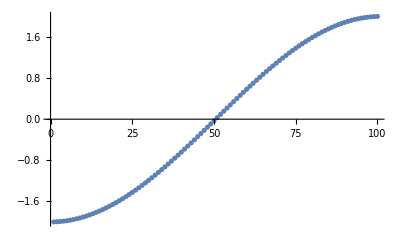

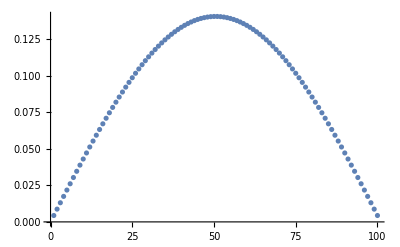
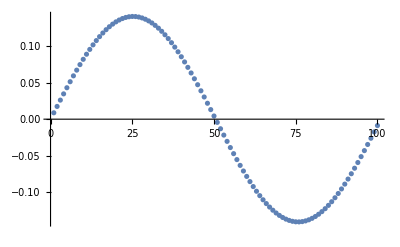
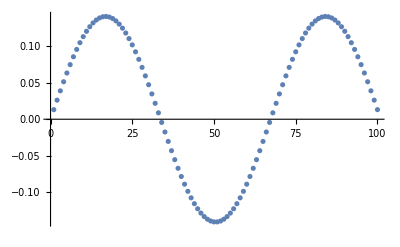
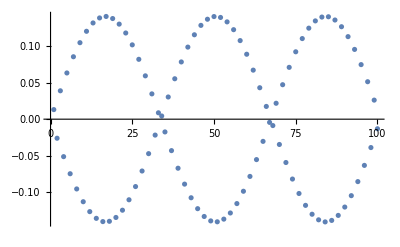
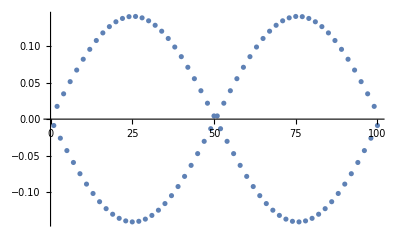
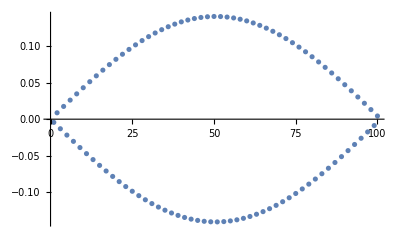

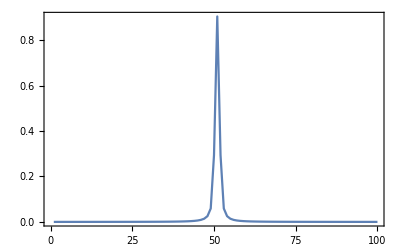

```mathematica
{EVals,EVecs}=Eigensystem[N[H[100]]];
sortedEVecs=(EVecs)[[Ordering[EVals]]];
sortedEVals=Sort[EVals];
ListPlot[sortedEVals]

{ListPlot[sortedEVecs[[1]]],ListPlot[sortedEVecs[[2]]],ListPlot[sortedEVecs[[3]]],ListPlot[sortedEVecs[[98]]],ListPlot[sortedEVecs[[99]]], ListPlot[sortedEVecs[[100]]]}

{ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[1]]]],50],PlotRange->All,Frame->True],
ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[2]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[3]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[100]]]],50],PlotRange->All,Frame->True]}
```

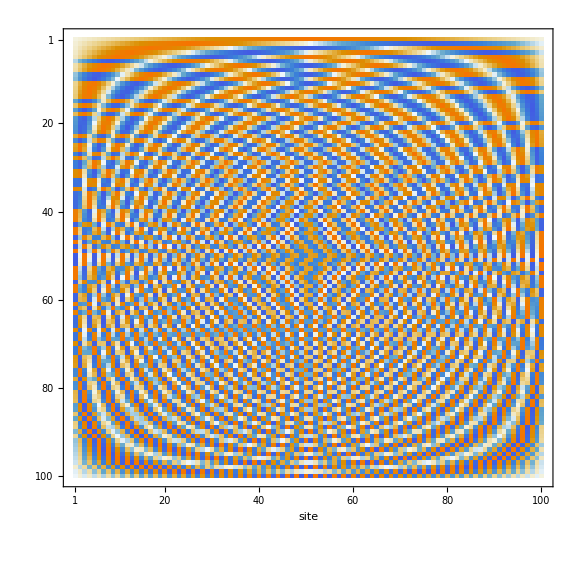

```mathematica
MatrixPlot[Table[sortedEVecs[[energy, site]], {energy, 1, Nl, 1},  {site, 1, Nl, 1}],  FrameLabel->{"","site"}, ImageSize->Large]
```

```mathematica
ClearAll@ψ;
H[Nl_]:=Table[If[Abs[i-j]==1,-1,0],{i,1,Nl},{j,1,Nl}];
Nl = 100;
tf = 15;
ψ0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== H[Nl] .ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

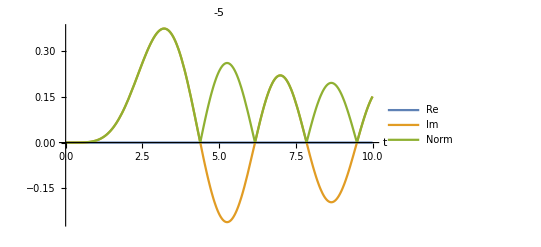
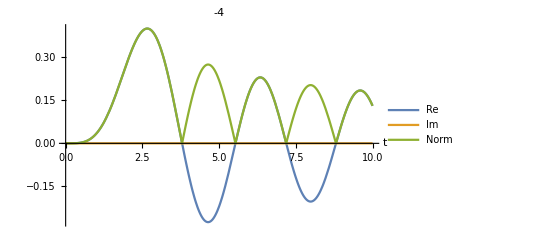
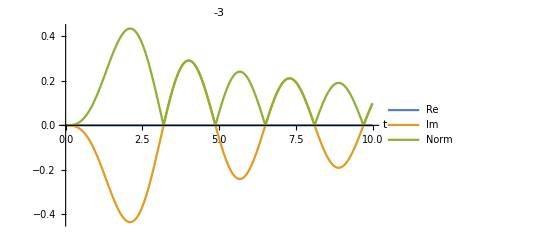
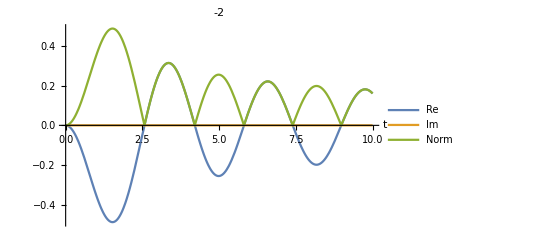
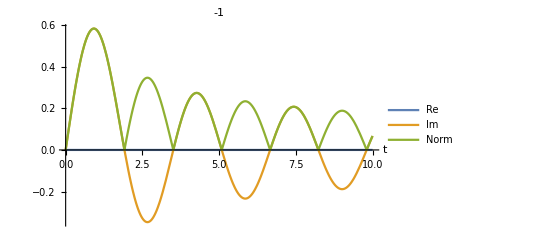
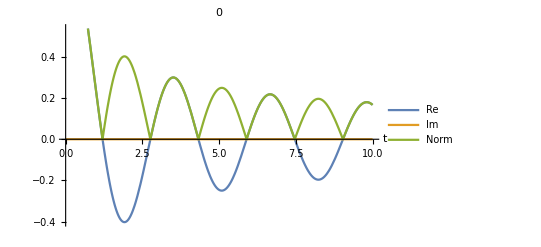
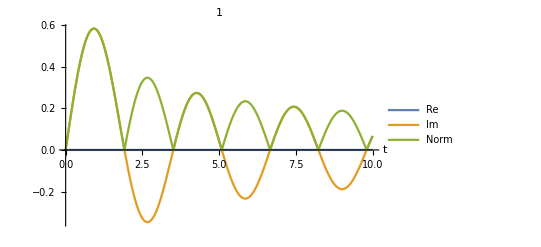
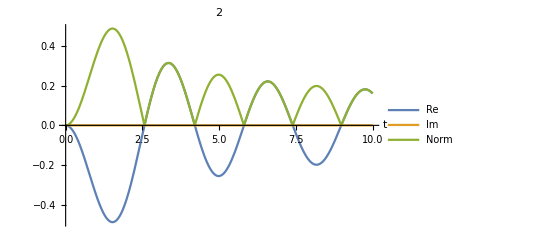

```mathematica
tmax = 10;
Table[Plot[{Re[ψ[t][[1, i]]], Im[ψ[t][[1, i]]], Norm[ψ[t][[1, i]]]}, {t, 0, tmax}, PlotLegends->{"Re","Im","Norm"}, AxesLabel->{"t", ""}, PlotLabel->i - Nl/2], {i, Nl/2-5, Nl/2+5}]
(*Manipulate[ListLinePlot[Abs[ψ[t]]^2,PlotRange->{0,1},PlotLabel->t],{t,0,5}]*)
```

```mathematica
sitenum = 98;
tmax = 10;
MatrixPlot[Table[Abs[ψ[t][[1, i]]], {t, 0, tmax, 0.1}, {i, Nl/2-sitenum/2, Nl/2+sitenum/2}], FrameLabel->{t,"site"}, ImageSize->Large, ColorFunctionScaling->False]
```

-Graphics-

### With Trap

Low ω

```mathematica
H[Nl_,ω_]:=Table[If[i==j,(i-Nl/2)^2 ω^2,If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
(*H[10,0.5]//MatrixForm*)
```

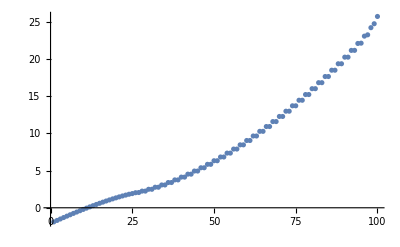

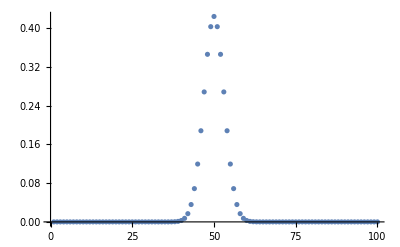
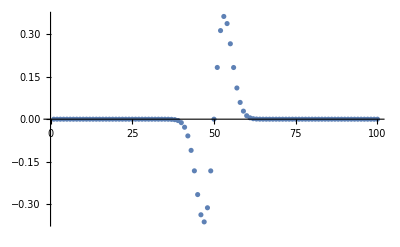
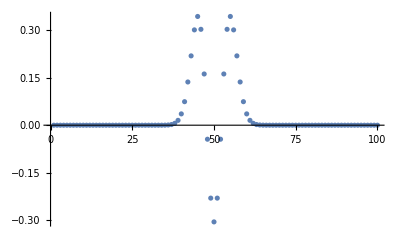
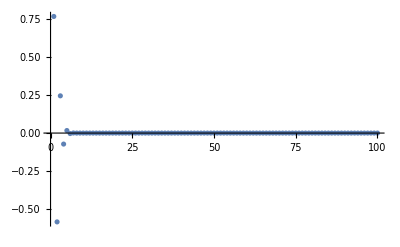
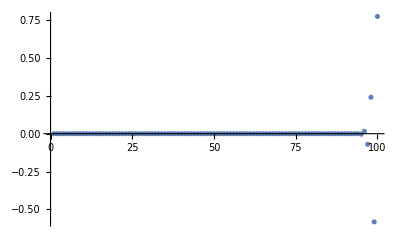

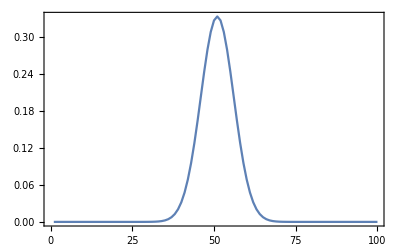
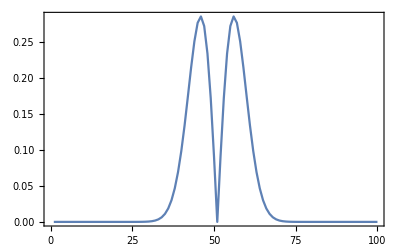

```mathematica
ω = 0.1;
Nl = 100;
{EVals,EVecs}=Eigensystem[N[H[Nl,ω]]];
sortedEVecs=(EVecs)[[Ordering[EVals]]];
sortedEVals=Sort[EVals];
ListPlot[sortedEVals]

{ListPlot[sortedEVecs[[1]],PlotRange->All],
ListPlot[sortedEVecs[[2]],PlotRange->All],
ListPlot[sortedEVecs[[3]],PlotRange->All],
ListPlot[sortedEVecs[[99]],PlotRange->All],
ListPlot[sortedEVecs[[100]],PlotRange->All]}

{ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[1]]]],50],PlotRange->All,Frame->True],
ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[2]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[3]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[100]]]],50],PlotRange->All,Frame->True]}
```

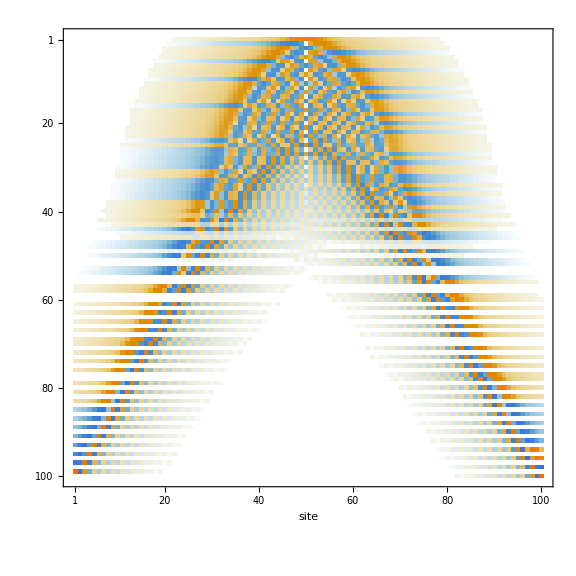

```mathematica
MatrixPlot[Table[sortedEVecs[[energy, site]], {energy, 1, Nl, 1},  {site, 1, Nl, 1}],  FrameLabel->{"","site"}, ImageSize->Large]
```

```mathematica
ClearAll@ψ;
H[Nl_,ω_]:=Table[If[i==j,(i-Nl/2)^2 ω^2,If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
ω = 0.1;
Nl = 100;
tf = 20;
ψ0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== H[Nl, ω] .ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

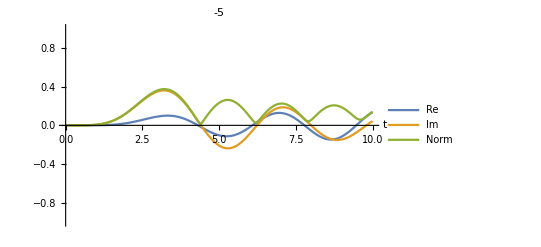
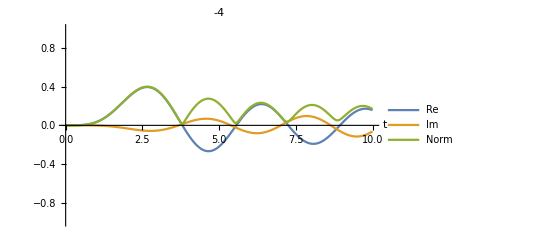
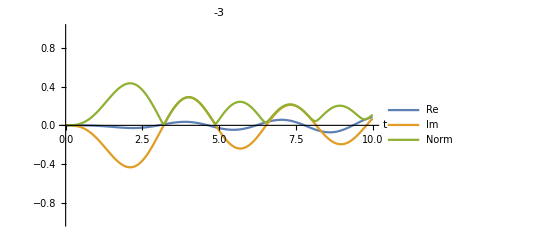
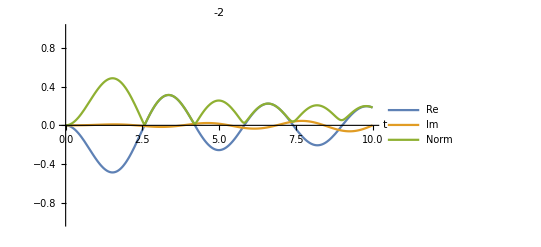
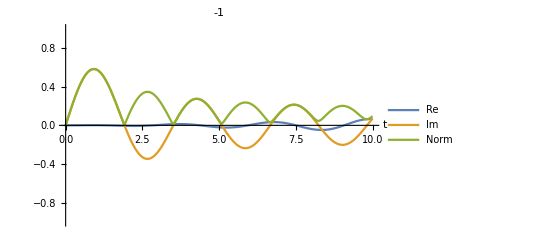
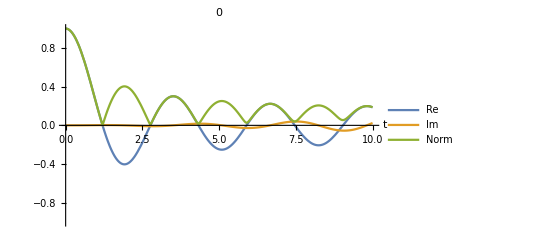
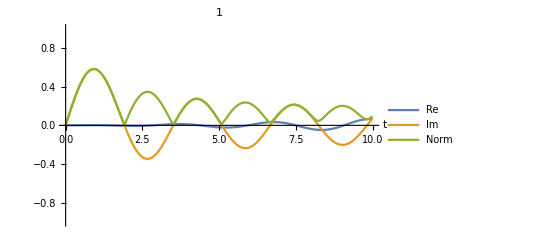
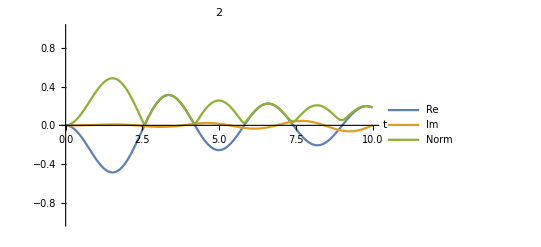

```mathematica
tmax = 10;
Table[Plot[{Re[ψ[t][[1, i]]], Im[ψ[t][[1, i]]], Norm[ψ[t][[1, i]]]}, {t, 0, tmax}, PlotLegends->{"Re","Im","Norm"},PlotRange ->{-1, 1}, AxesLabel->{"t", ""}, PlotLabel->i-Nl/2], {i, Nl/2-5, Nl/2+5}]
```

```mathematica
sitenum = 98;
tmax = 10;
MatrixPlot[Table[Abs[ψ[t][[1, i]]], {t, 0, tmax, 0.1}, {i, Nl/2-sitenum/2, Nl/2+sitenum/2}], FrameLabel->{"t (100ms)","site"},  ImageSize->Large, ColorFunctionScaling->False]
```

-Graphics-

High ω

```mathematica
H[Nl_,ω_]:=Table[If[i==j,(i-Nl/2)^2 ω^2,If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
ω = 0.6;
Nl = 100;
{EVals,EVecs}=Eigensystem[N[H[Nl,ω]]];
sortedEVecs=(EVecs)[[Ordering[EVals]]];
sortedEVals=Sort[EVals];

(*ListPlot[sortedEVals]

{ListPlot[sortedEVecs[[1]],PlotRange->All],
ListPlot[sortedEVecs[[2]],PlotRange->All],
ListPlot[sortedEVecs[[3]],PlotRange->All],
ListPlot[sortedEVecs[[99]],PlotRange->All],
ListPlot[sortedEVecs[[100]],PlotRange->All]}

{ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[1]]]],50],PlotRange->All,Frame->True],
ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[2]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[3]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[100]]]],50],PlotRange->All,Frame->True]}*)
```

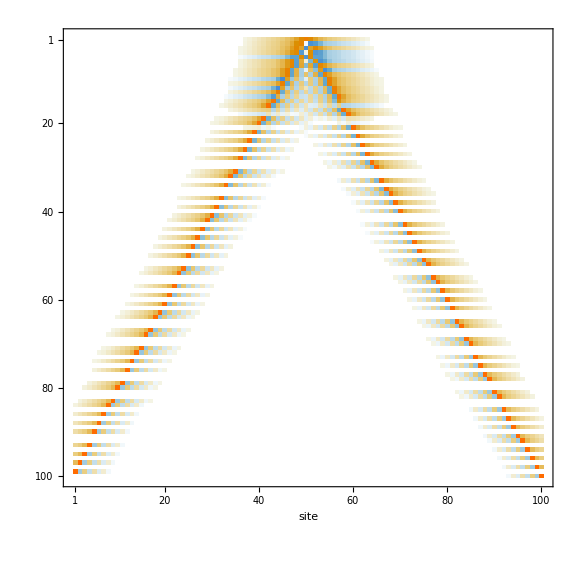

```mathematica
MatrixPlot[Table[sortedEVecs[[energy, site]], {energy, 1, Nl, 1},  {site, 1, Nl, 1}],  FrameLabel->{"","site"}, ImageSize->Large]
```

```mathematica
ClearAll@ψ;
H[Nl_,ω_]:=Table[If[i==j,(i-Nl/2)^2 ω^2,If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
ω = 0.6;
Nl = 100;
tf = 20;
ψ0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== H[Nl, ω] .ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

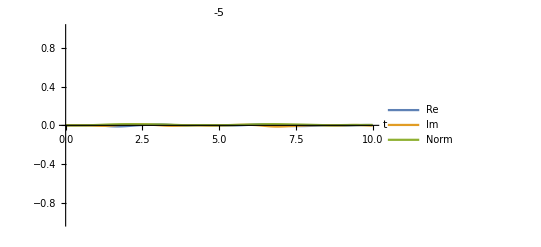
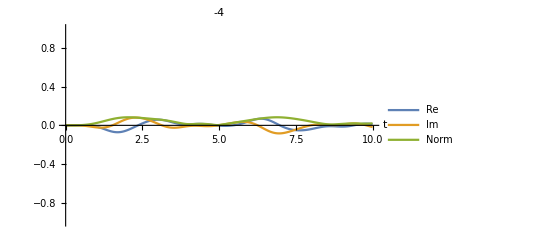
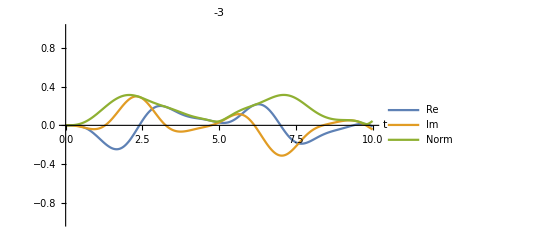
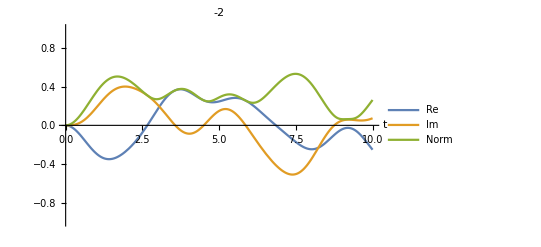
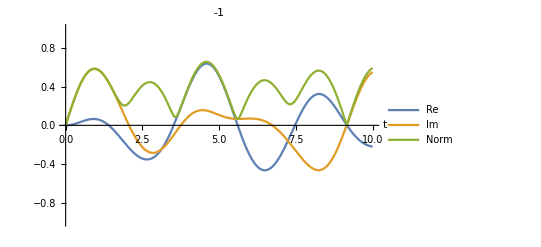
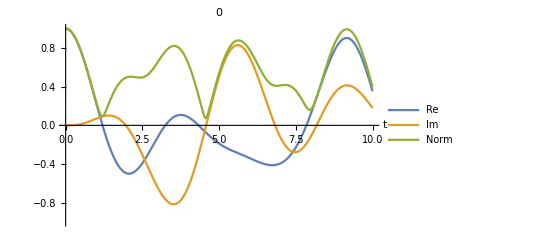
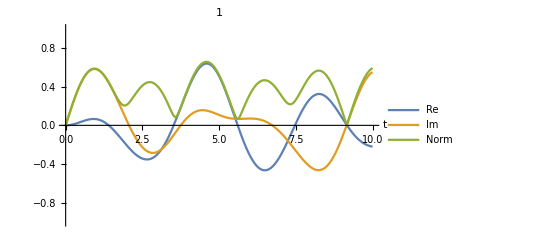
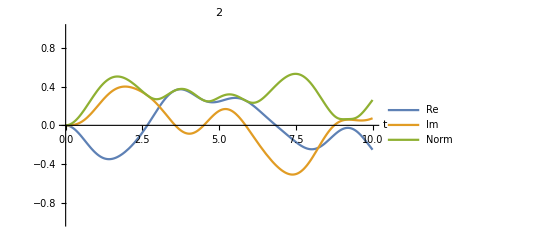

```mathematica
tmax = 10;
Table[Plot[{Re[ψ[t][[1, i]]], Im[ψ[t][[1, i]]], Norm[ψ[t][[1, i]]]}, {t, 0, tmax}, PlotLegends->{"Re","Im","Norm"},PlotRange ->{-1, 1}, AxesLabel->{"t", ""}, PlotLabel->i-Nl/2], {i, Nl/2-5, Nl/2+5}]
```

```mathematica
sitenum = 98;
tmax = 10;
MatrixPlot[Table[Abs[ψ[t][[1, i]]], {t, 0, tmax, 0.1}, {i, Nl/2-sitenum/2, Nl/2+sitenum/2}], FrameLabel->{"t (100ms)","site"},  ImageSize->Large, ColorFunctionScaling->False]
```

-Graphics-

#### With force term

```mathematica
H[Nl_, F_]:=Table[If[i==j,F*i,If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
(*H[10,0.5]//MatrixForm*)
```

#### Small force

```mathematica
Nl = 100;
F = 0.01;
{EVals,EVecs}=Eigensystem[N[H[100, F]]];
sortedEVecs=(EVecs)[[Ordering[EVals]]];
sortedEVals=Sort[EVals];
(*ListPlot[sortedEVals]

{ListPlot[sortedEVecs[[1]],PlotRange->All],
ListPlot[sortedEVecs[[2]],PlotRange->All],
ListPlot[sortedEVecs[[3]],PlotRange->All],
ListPlot[sortedEVecs[[99]],PlotRange->All],
ListPlot[sortedEVecs[[100]],PlotRange->All]}

{ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[1]]]],50],PlotRange->All,Frame->True],
ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[2]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[3]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[100]]]],50],PlotRange->All,Frame->True]}*)
```

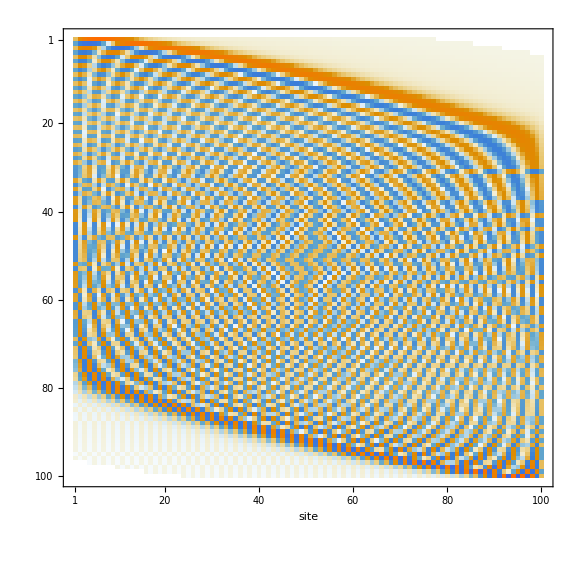

```mathematica
MatrixPlot[Table[sortedEVecs[[energy, site]], {energy, 1, Nl, 1},  {site, 1, Nl, 1}],  FrameLabel->{"","site"}, ImageSize->Large]
```

```mathematica
ClearAll@ψ;
H[Nl_, F_]:=Table[If[i==j,F*i,If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
Nl = 100;
tf = 10;
F = 0.01;
ψ0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== H[Nl, F] .ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

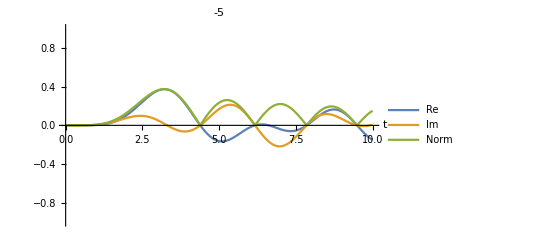
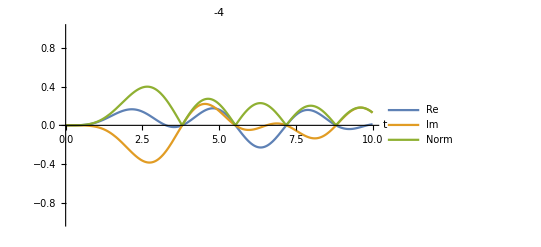
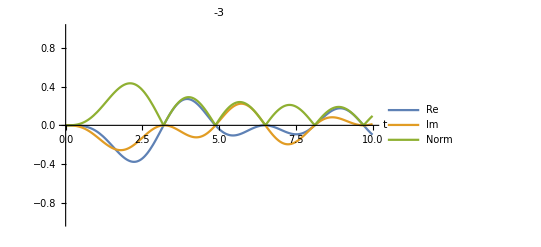
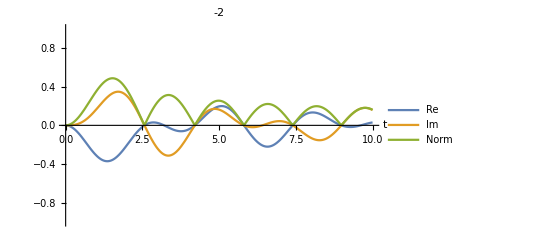
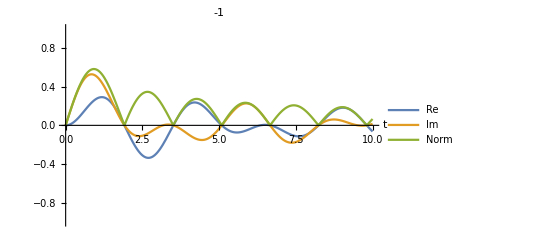
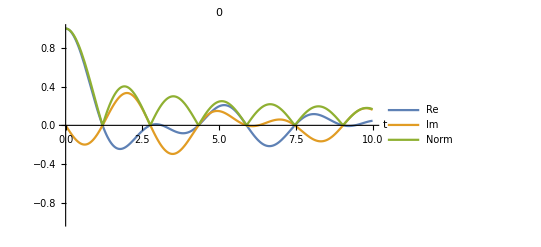
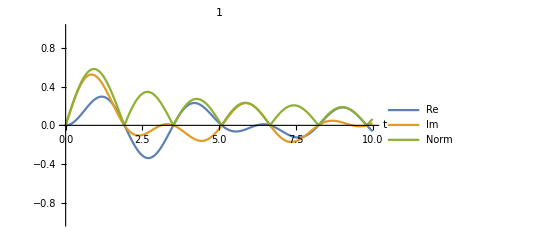
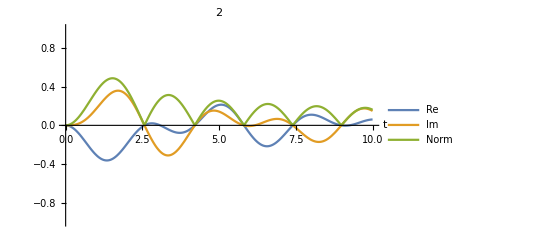

```mathematica
tmax = 10;
Table[Plot[{Re[ψ[t][[1, i]]], Im[ψ[t][[1, i]]], Norm[ψ[t][[1, i]]]}, {t, 0, tmax}, PlotLegends->{"Re","Im","Norm"}, PlotRange ->{-1, 1},AxesLabel->{"t", ""}, PlotLabel->i - Nl/2], {i, Nl/2 - 5, Nl/2+5}]
```

```mathematica
(*λ[t_]:= MatrixExp[I H[Nl] t].ψ0;
Table[Plot[{Re[λ[t][[ i]]], Im[λ[t][[ i]]], Norm[λ[t][[i]]]}, {t, 0, tf}, PlotLegends->{"Re","Im","Norm"}, AxesLabel->{"t", ""}, PlotLabel->i], {i, 1, Nl}]*)
```

```mathematica
sitenum = 98;
tmax = 10;
MatrixPlot[Table[Abs[ψ[t][[1, i]]], {t, 0, tmax, 0.1}, {i, Nl/2-sitenum/2, Nl/2+sitenum/2}], FrameLabel->{"t (100ms)","site"}, ImageSize->Large, ColorFunctionScaling->False]
```

-Graphics-

#### Larger force

```mathematica
Nl = 100;
F = 0.7;
{EVals,EVecs}=Eigensystem[N[H[100, F]]];
sortedEVecs=(EVecs)[[Ordering[EVals]]];
sortedEVals=Sort[EVals];
(*ListPlot[sortedEVals]

{ListPlot[sortedEVecs[[1]],PlotRange->All],
ListPlot[sortedEVecs[[2]],PlotRange->All],
ListPlot[sortedEVecs[[3]],PlotRange->All],
ListPlot[sortedEVecs[[99]],PlotRange->All],
ListPlot[sortedEVecs[[100]],PlotRange->All]}

{ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[1]]]],50],PlotRange->All,Frame->True],
ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[2]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[3]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[100]]]],50],PlotRange->All,Frame->True]}*)
```

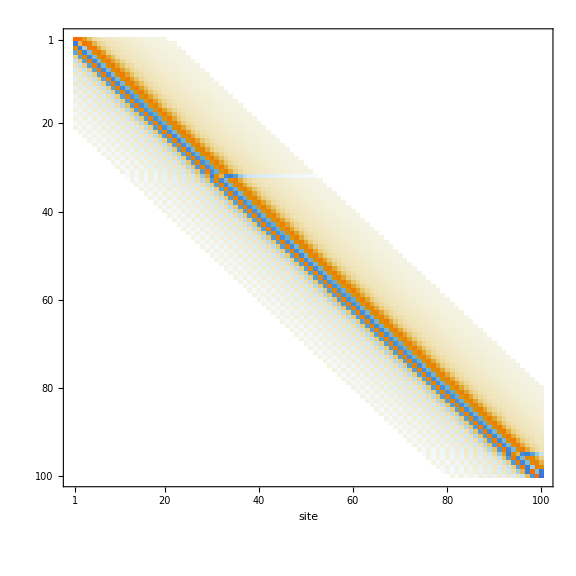

```mathematica
MatrixPlot[Table[sortedEVecs[[energy, site]], {energy, 1, Nl, 1},  {site, 1, Nl, 1}],  FrameLabel->{"","site"}, ImageSize->Large]
```

```mathematica
ClearAll@ψ;
H[Nl_, F_]:=Table[If[i==j,F*i,If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
Nl = 100;
tf = 10;
F = 0.7;
ψ0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== H[Nl, F] .ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

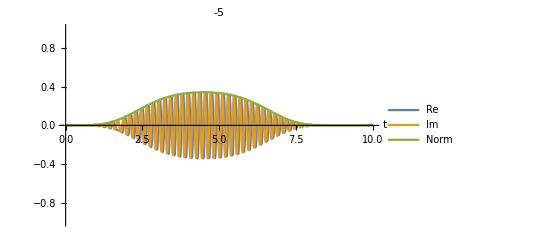
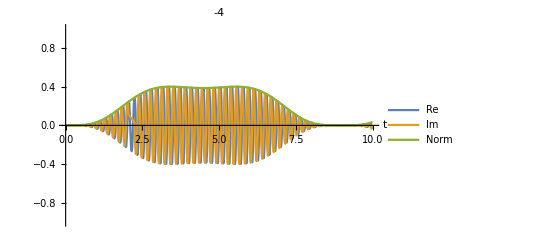
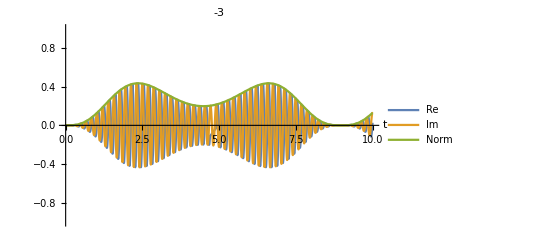
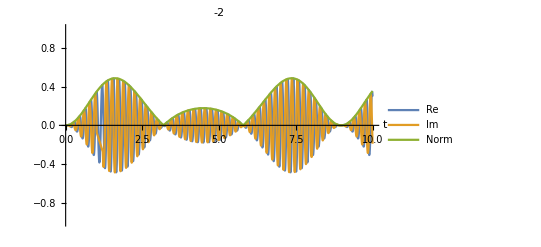
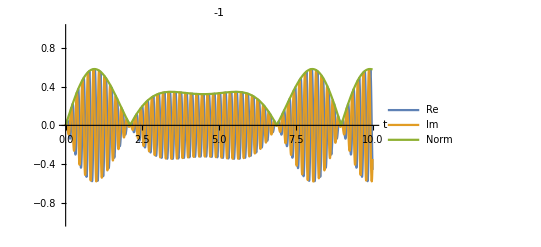
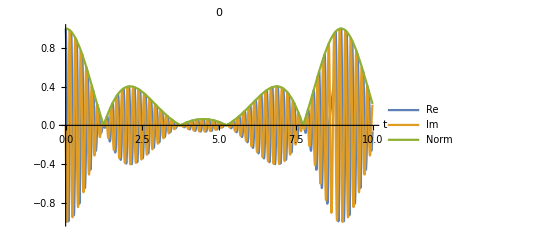
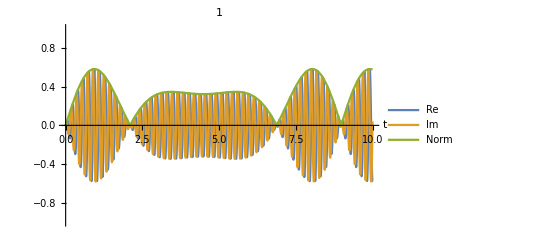
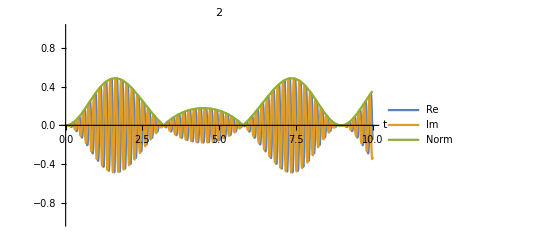

```mathematica
tmax = 10;
Table[Plot[{Re[ψ[t][[1, i]]], Im[ψ[t][[1, i]]], Norm[ψ[t][[1, i]]]}, {t, 0, tmax}, PlotLegends->{"Re","Im","Norm"}, PlotRange ->{-1, 1},AxesLabel->{"t", ""}, PlotLabel->i - Nl/2], {i, Nl/2 - 5, Nl/2+5}]
```

```mathematica
sitenum = 98;
tmax = 10;
MatrixPlot[Table[Abs[ψ[t][[1, i]]], {t, 0, tmax, 0.1}, {i, Nl/2-sitenum/2, Nl/2+sitenum/2}], FrameLabel->{"t (100ms)","site"}, ImageSize->Large, ColorFunctionScaling->False]
```

-Graphics-

#### Time dependent force term - NDSolve

```mathematica
Ht[Nl_,ω_, F_, t_]:=Table[If[i==j, F*i*Cos[ω*t],If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
(*Ht[10,0.5, 0.5, t]//MatrixForm*)
```

#### Low freq, Low A

```mathematica
ClearAll@ψ;
Ht[Nl_,ω_, F_, t_]:=Table[If[i==j, A*i*Cos[ω*t],If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
Nl = 100;
tf = 10;
ω = 0.1;
A= 0.1;
ψ0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== Ht[Nl, A, ω, t] .ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

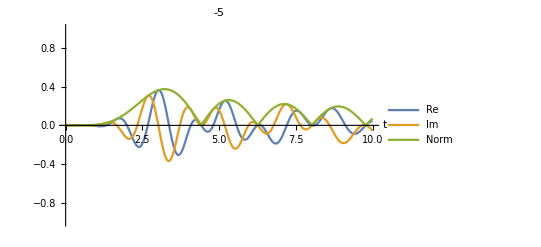
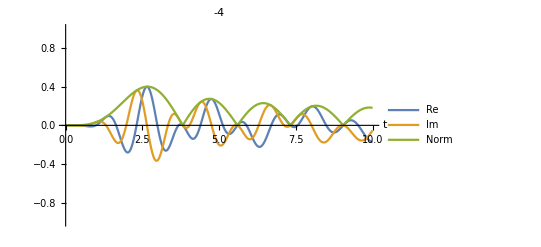
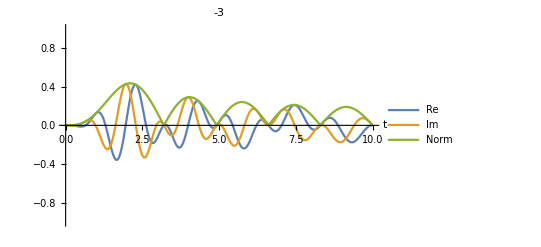
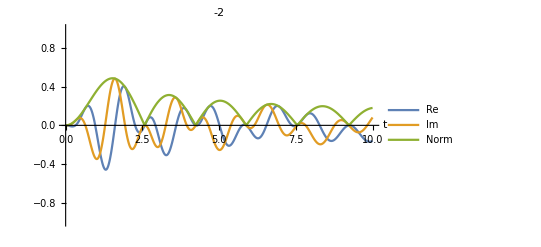
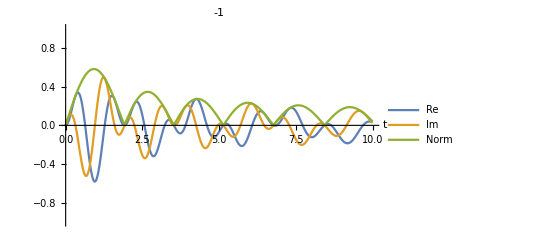
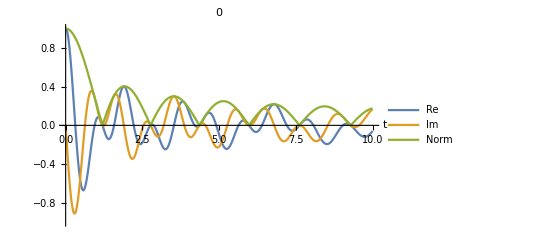
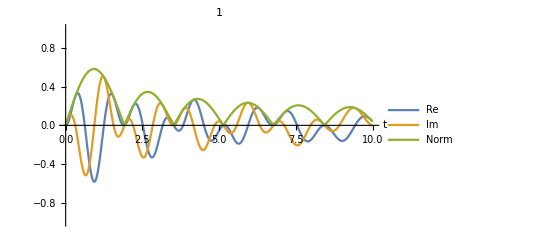
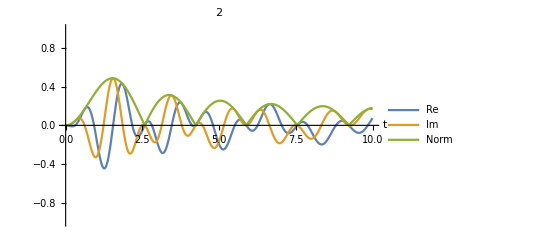

```mathematica
tmax = 10;
Table[Plot[{Re[ψ[t][[1, i]]], Im[ψ[t][[1, i]]], Norm[ψ[t][[1, i]]]}, {t, 0, tmax}, PlotLegends->{"Re","Im","Norm"},PlotRange ->{-1, 1}, AxesLabel->{"t", ""}, PlotLabel->i - Nl/2], {i, Nl/2 - 5, Nl/2 + 5}]
```

```mathematica
sitenum = 98;
tmax = 10;
MatrixPlot[Table[Abs[ψ[t][[1, i]]], {t, 0, tmax, 0.1}, {i, Nl/2-sitenum/2, Nl/2+sitenum/2}], FrameLabel->{"t (100ms)","site"}, ImageSize->Large, ColorFunctionScaling->False]
```

-Graphics-

#### Low freq, High A

```mathematica
ClearAll@ψ;
Ht[Nl_,ω_, A_, t_]:=Table[If[i==j, A*i*Cos[ω*t],If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
Nl = 100;
tf = 10;
ω = 0.1;
A = 5;
ψ0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== Ht[Nl, A, ω, t] .ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

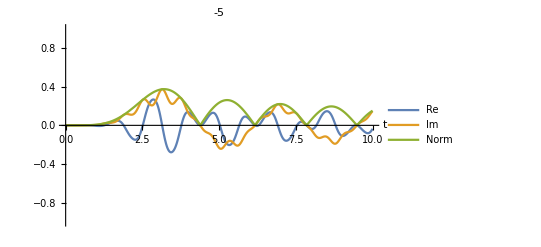
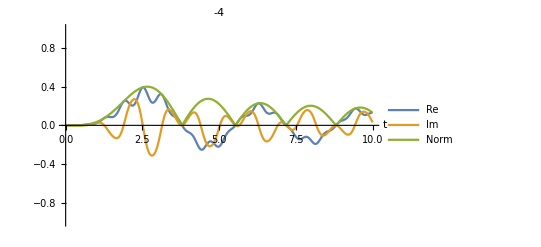
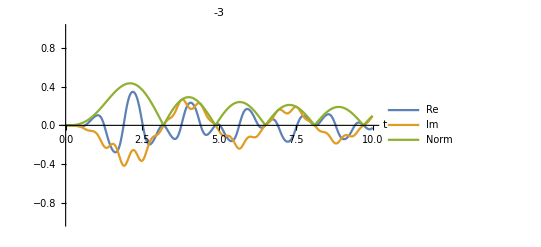
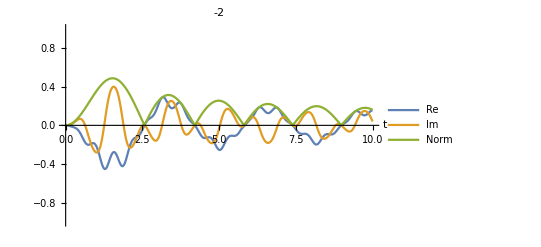
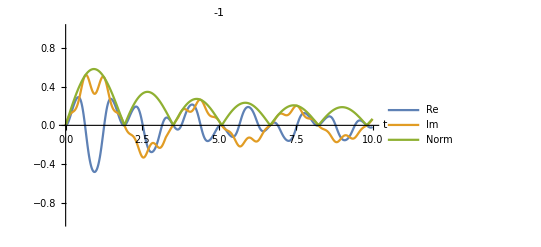
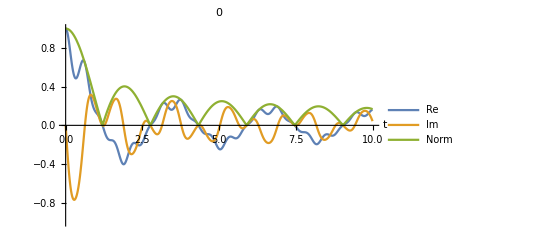
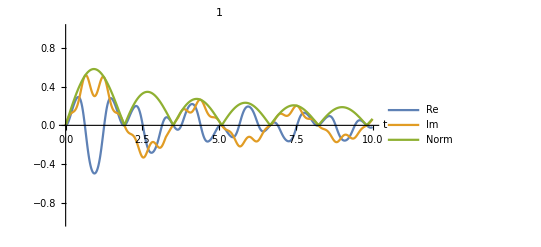
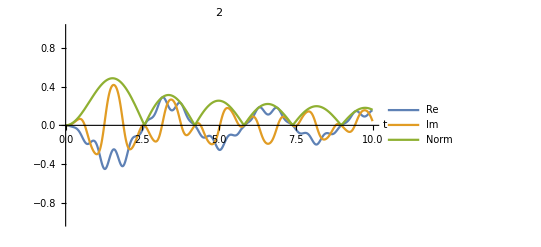

```mathematica
tmax = 10;
Table[Plot[{Re[ψ[t][[1, i]]], Im[ψ[t][[1, i]]], Norm[ψ[t][[1, i]]]}, {t, 0, tmax}, PlotLegends->{"Re","Im","Norm"},PlotRange ->{-1, 1}, AxesLabel->{"t", ""}, PlotLabel->i - Nl/2], {i, Nl/2 - 5, Nl/2 + 5}]
```

```mathematica
sitenum = 98;
tmax = 10;
MatrixPlot[Table[Abs[ψ[t][[1, i]]], {t, 0, tmax, 0.1}, {i, Nl/2-sitenum/2, Nl/2+sitenum/2}], FrameLabel->{"t (100ms)","site"}, ImageSize->Large, ColorFunctionScaling->False]
```

-Graphics-

#### High freq, low A

```mathematica
ClearAll@ψ;
Ht[Nl_,ω_, A_, t_]:=Table[If[i==j, A*i*Cos[ω*t],If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
Nl = 100;
tf = 10;
ω = 1;
A = 0.1;
ψ0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== Ht[Nl, A, ω, t] .ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

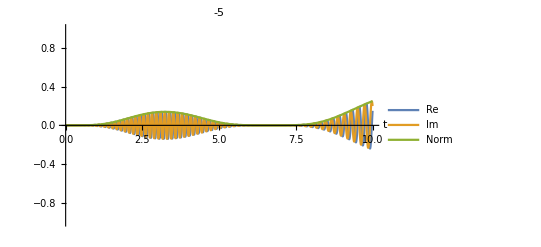
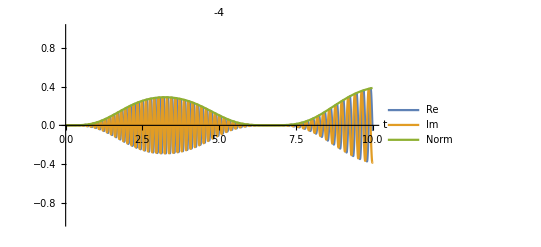
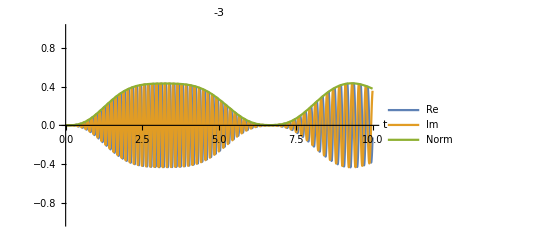
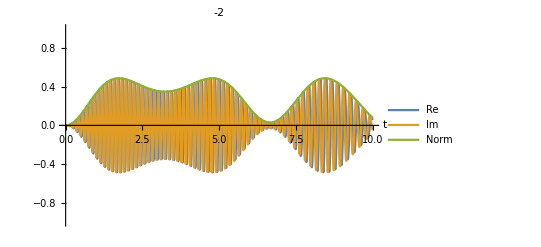
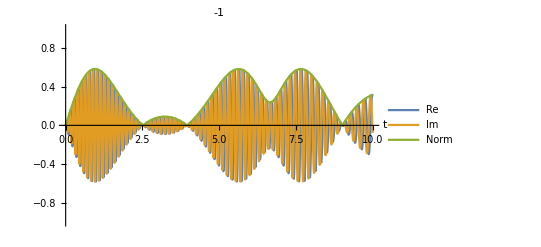
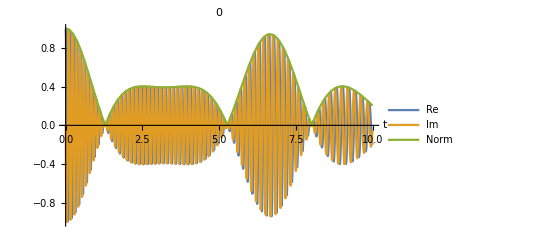
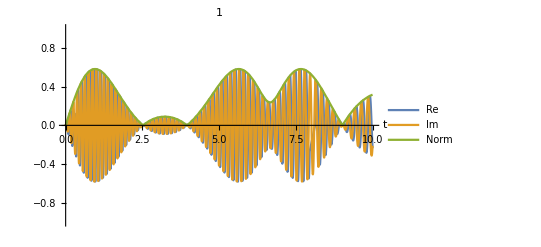
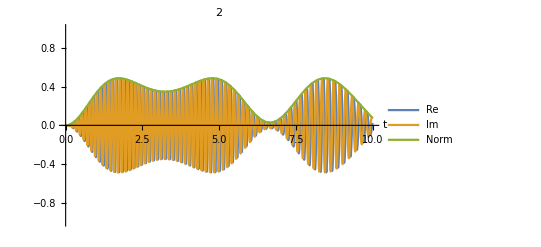

```mathematica
tmax = 10;
Table[Plot[{Re[ψ[t][[1, i]]], Im[ψ[t][[1, i]]], Norm[ψ[t][[1, i]]]}, {t, 0, tmax}, PlotLegends->{"Re","Im","Norm"},PlotRange ->{-1, 1}, AxesLabel->{"t", ""}, PlotLabel->i - Nl/2], {i, Nl/2 - 5, Nl/2 + 5}]
```

```mathematica
sitenum = 98;
tmax = 10;
MatrixPlot[Table[Abs[ψ[t][[1, i]]], {t, 0, tmax, 0.1}, {i, Nl/2-sitenum/2, Nl/2+sitenum/2}], FrameLabel->{"t (100ms)","site"}, ImageSize->Large, ColorFunctionScaling->False]
```

-Graphics-

#### High freq, high A

```mathematica
ClearAll@ψ;
Ht[Nl_,ω_, A_, t_]:=Table[If[i==j, A*i*Cos[ω*t],If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
Nl = 100;
tf = 10;
ω = 1;
A = 3;
ψ0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== Ht[Nl, A, ω, t] .ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

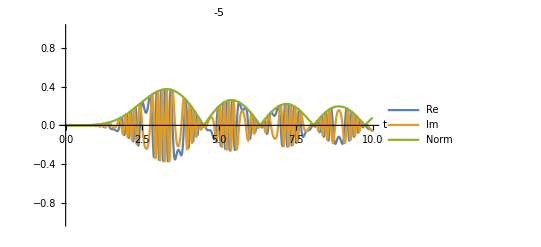
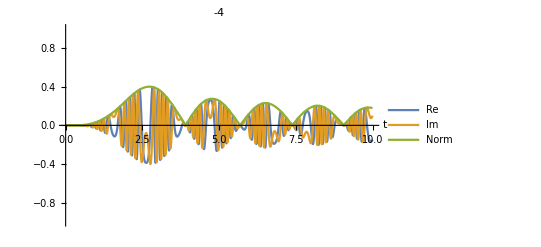
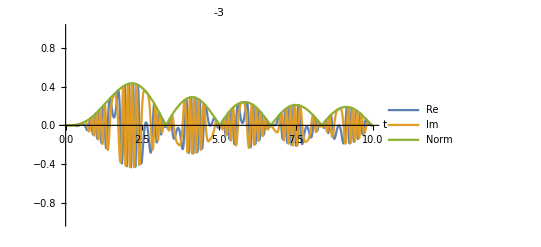
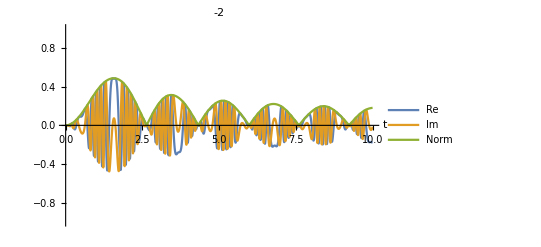
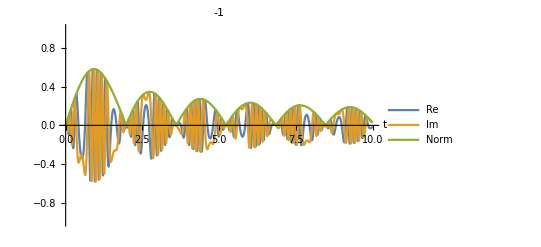
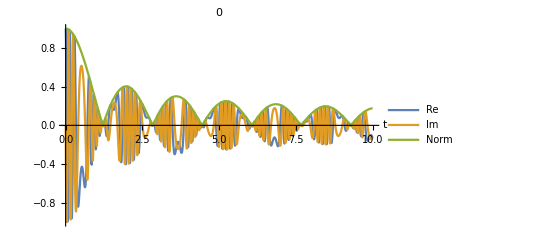
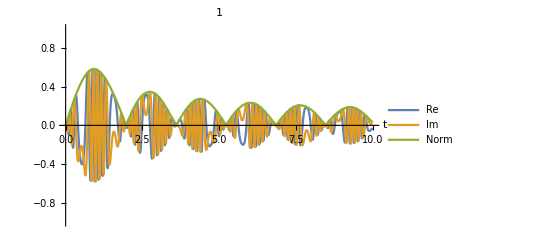
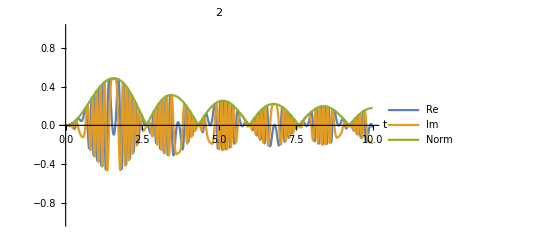

```mathematica
tmax = 10;
Table[Plot[{Re[ψ[t][[1, i]]], Im[ψ[t][[1, i]]], Norm[ψ[t][[1, i]]]}, {t, 0, tmax}, PlotLegends->{"Re","Im","Norm"},PlotRange ->{-1, 1}, AxesLabel->{"t", ""}, PlotLabel->i - Nl/2], {i, Nl/2 - 5, Nl/2 + 5}]
```

```mathematica
sitenum = 98;
tmax = 10;
MatrixPlot[Table[Abs[ψ[t][[1, i]]], {t, 0, tmax, 0.1}, {i, Nl/2-sitenum/2, Nl/2+sitenum/2}], FrameLabel->{"t (100ms)","site"}, ImageSize->Large, ColorFunctionScaling->False]
```

-Graphics-

#### Random below..

```mathematica
(*Table[Plot[{Re[ψ[t][[i]]/.s], Im[ψ[t][[i]]/.s],Norm[ψ[t][[i]]/.s]}, {t, 0, 1}, PlotLegends->{"Re","Im","Norm"}], {i, 1, Nl}]
Table[Plot[{Re[ψ[t][[i]]/.s], Im[ψ[t][[i]]/.s],Abs[ψ[t][[i]]/.s],Norm[ψ[t][[i]]/.s]}, {i, 1, Nl}], {t, 0, 1, 0.1}]*)
```

```mathematica
tt = Range[0, 1, 0.1]
ww = Flatten[Evaluate[Abs[ψ[#]] /. s]] &/@ tt
Plot[ tt, ww[[All, 2]] ]
(*ListPlot[Table[Transpose[{tt, ww[[All, i]]}], {i, 3}]]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

{{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{4.15962×10^-6,0.000166245,0.00498335,0.0995007,0.990025,0.0995007,0.00498335,0.000166245,4.1582×10^-6,8.34361×10^-8},{0.0000662139,0.00132003,0.0197345,0.196026,0.960398,0.196026,0.0197345,0.00132004,0.0000661251,2.65111×10^-6},{0.000332449,0.0043995,0.0436643,0.286699,0.912006,0.286699,0.0436644,0.00439955,0.000331447,0.0000199874},{0.00103847,0.010246,0.0758154,0.368837,0.846292,0.368837,0.0758154,0.0102463,0.0010329,0.0000833934},{0.0024973,0.0195605,0.114898,0.440042,0.765209,0.440042,0.114898,0.019562,0.00247628,0.000251213},{0.00508345,0.0328656,0.159339,0.498277,0.671155,0.498277,0.159339,0.032871,0.00502154,0.000615288},{0.00921334,0.0504753,0.20734,0.541935,0.566894,0.541935,0.207338,0.0504908,0.00905977,0.00130516},{0.0153233,0.0724723,0.256945,0.569885,0.455463,0.569885,0.256941,0.072511,0.0149876,0.00248993},{0.0238457,0.098695,0.306117,0.581513,0.340075,0.581514,0.306107,0.0987815,0.0231796,0.00437753},{0.0351842,0.128736,0.352809,0.576736,0.224011,0.576738,0.352787,0.128913,0.0339609,0.00721095}}

Plot::pllim: Range specification {0.,0.000166245,0.00132003,0.0043995,0.010246,0.0195605,0.0328656,0.0504753,0.0724723,0.098695,0.128736} is not of the form {x, xmin, xmax}.

Plot[tt,ww⟦All,2⟧]

#### Create U

```mathematica
ClearAll@constructU;
constructU[h_, tinit_, tfinal_, n_] := Module[{dt = N[(tfinal - tinit)/n],
curVal = IdentityMatrix[Length@h[0]]},
Do[curVal = MatrixExp[-I*h[t]*dt].curVal, {t, tinit, tfinal - dt, dt}];
curVal]

Nl = 10;
psi0 = Table[If[i==Nl/2,1,0],{i,1,Nl}];

constructU[Ht[Nl, 0.01, 0. 10], 0, 0.1, 10].psi0
(*ListLinePlot[Chop[constructU[Ht[Nl,0.01, 0, 10], 0, 0.1, 10]].psi0, PlotRange->All]*)
(*ListPlot[sortedEVecs[[1]],PlotRange->All],*)
```

```mathematica
ListPlot[
Table[Chop[constructU[Ht[Nl, 0.01, 0.01, #].psi0 &, 0, upt, 100]],
{upt, .1, 1, .1}
],
Joined->True,
PlotRange->{-1, 1}
]
```

```mathematica
ListPlot[
Table[
Chop[#] &@(constructU[
Ht[Nl, 0.05, F, #] &, 0, upt, 100].psi0),
{upt, .01, 20, .1}
],
Joined->True,
PlotRange->{-1, 1}
]
```

```mathematica
ham[e1_, e2_, b_, omega_, t_]:= {{e1, b*Cos[omega*t]}, {b*Cos[omega*t], e2}};
Module[{ψ, sol, tmax = 20}, 
sol = NDSolve[{I D[ψ[t], t]== Ht[10,0.05,0.05, t] .ψ[t], ψ[0] == psi0}, ψ, {t, 0, tMax}];
```

```mathematica
Module[{ψ, sol, tmax = 20}, 
sol = First@NDSolve[{I D[ψ[t], t]==
Ht[10,0.05, 0.05, t] .ψ[t], ψ[0] == psi0}, ψ, {t, 0, tMax}];
Plot[Chop[#*.PauliMatrix[3].#] &@(ψ /. sol)[t],
{t, 0, tMax}, PlotRange-> {-1, 1}]
]
```

### Create U (2x2)

```mathematica
ham[e1_, e2_, b_, omega_, t_]:= {{e1, b*Cos[omega*t]}, {b*Cos[omega*t], e2}}

ClearAll@constructU;
constructU[h_, tinit_, tfinal_, n_] := Module[{dt = N[(tfinal - tinit)/n],
curVal = IdentityMatrix[Length@h[0]]},
Do[curVal = MatrixExp[-I*h[t]*dt].curVal, {t, tinit, tfinal - dt, dt}];
curVal]

ClearAll[cU, psi0];
psi0 = {1., 0};
Manipulate[
ListPlot[
Table[
Chop[#*.PauliMatrix[3].#] &@(constructU[
ham[-1., 1., b, 1., #] &, 0, upt, 100].psi0),
{upt, .01, 20, .1}
],
Joined->True,
PlotRange->{-1, 1}
],
{b, 0, 2}
]
```

#### NDsolve (2x2)

```mathematica
Manipulate[Module[{ψ, sol, tmax = 20}, 
sol = First@NDSolve[{I D[ψ[t], t]==
ham[-1, 1, b, 1, t] .ψ[t], ψ[0] == {1, 0}}, ψ, {t, 0, 1}];
Plot[Chop[#*.PauliMatrix[3].#] &@(ψ /. sol)[t],
{t, 0, 1}, PlotRange-> {-1, 1}]
],
{{b, 1}, 0, 2}
]
```

NDSolve::underdet: There are more dependent variables, {ham[-1,1,2.,1,t],ψ$3484[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {ⅈ ψ$3484'[0.0000204286]==ham[-1,1,2.,1,0.0000204286].ψ$3484[0.0000204286],ψ$3484[0]=={1,0}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {(0.+1. ⅈ) ψ$3484'[0.0000204286]==ham[-1.,1.,2.,1.,0.0000204286].ψ$3484[0.0000204286],ψ$3484[0.]=={1.,0.}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {(0.+1. ⅈ) ψ$3484'[0.0000204286]==ham[-1.,1.,2.,1.,0.0000204286].ψ$3484[0.0000204286],ψ$3484[0.]=={1.,0.}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

NDSolve::underdet: There are more dependent variables, {ham[-1,1,2.,1,t],ψ$23790[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {ⅈ ψ$23790'[0.0000204286]==ham[-1,1,2.,1,0.0000204286].ψ$23790[0.0000204286],ψ$23790[0]=={1,0}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {(0.+1. ⅈ) ψ$23790'[0.0000204286]==ham[-1.,1.,2.,1.,0.0000204286].ψ$23790[0.0000204286],ψ$23790[0.]=={1.,0.}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {(0.+1. ⅈ) ψ$23790'[0.0000204286]==ham[-1.,1.,2.,1.,0.0000204286].ψ$23790[0.0000204286],ψ$23790[0.]=={1.,0.}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

NDSolve::underdet: There are more dependent variables, {ham[-1,1,2.,1,t],ψ$4910[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {ⅈ ψ$4910'[0.0000204286]==ham[-1,1,2.,1,0.0000204286].ψ$4910[0.0000204286],ψ$4910[0]=={1,0}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {(0.+1. ⅈ) ψ$4910'[0.0000204286]==ham[-1.,1.,2.,1.,0.0000204286].ψ$4910[0.0000204286],ψ$4910[0.]=={1.,0.}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {(0.+1. ⅈ) ψ$4910'[0.0000204286]==ham[-1.,1.,2.,1.,0.0000204286].ψ$4910[0.0000204286],ψ$4910[0.]=={1.,0.}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.